```mathematica
Datos
```

```mathematica
Ni=50;
β=10^6;       
Ci=4.88;
Di=0.43;
ηLos=10^(0.1/10);
ηNLos=10^(21/10);
VC=3 10^8;
fc=2.5 10^9;
No=2.0019 10^-12;
Ki=1;
B=50 10^6;
Lxti=0;
Lxts=500;
Lyti=0;
Lyts=500;
Lzti=0;
Lzts=1;
Lxs=500;
Lys=500;
Lxi=0;
Lyi=0;
Lzi=0;
Lzs=1;
α =2;
λ = 0.01;
h =10;
```

## Li and Joint

```mathematica
jointPDF3D[Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,x_,y_,z_,λ_]:=PDF[ProductDistribution[TruncatedDistribution[{Lxti,Lxts},ExponentialDistribution[λ]],TruncatedDistribution[{Lyti,Lyts},ExponentialDistribution[λ]],TruncatedDistribution[{Lzti,Lzts},ExponentialDistribution[λ]]],{x,y,z}]
di[x_,xi_,y_,yi_,z_,hi_]:=Sqrt[(xi-x)^2+(yi-y)^2+(hi-z)^2];
βeta[x_,xi_,y_,yi_,z_,hi_]:=180/π ArcSin[(hi*Sqrt[(xi-x)^2+(yi-y)^2])/(di[x,xi,y,yi,z,hi] Sqrt[(xi-x)^2+(yi-y)^2+z^2])] ;
Plos[x_,xi_,y_,yi_,hi_,z_,Ci_,Di_]:=1/(1+Ci ⅇ^(-Di ( βeta[x,xi,y,yi,z,hi]-Ci))) ;

Li1[x_,xi_,y_,yi_,hi_,z_,Ci_,Di_,ηLos_,ηNLos_,fc_,VC_]:=Plos[x,xi,y,yi,hi,z,Ci,Di] *((4 Pi fc)/VC)^2 *di[x,xi,y,yi,z,hi]^α *ηLos +( ηNLos *(1- Plos[x,xi,y,yi,hi,z,Ci,Di])*di[x,xi,y,yi,z,hi]^α *((4 Pi fc)/VC)^2) ;

Mi[Ni_,Lxs_,Lys_,Lxi_,Lyi_,Lzs_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,λ_]:= Ni* Abs[NIntegrate[jointPDF3D[Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,x,y,z,λ],{x,Lxi,Lxs},{y,Lyi,Lys},{z,Lzi,Lzs}]];
```

## Función Objetivo

```mathematica
ptG3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,β_,B_ ,Ni_,x_,y_,z_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_,λ_]:=(2^((β Mi[Ni,Lxs,Lys,Lxi,Lyi,Lzs,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,λ])/B)-1)*No* Li1[x,xi,y,yi,z,hi,Ci,Di,ηLos,ηNLos,fc,VC]*jointPDF3D[Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,x,y,z,λ];

ptGNint3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_,λ_]:=NIntegrate[ptG3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B, Ni,x,y,z,xi,yi,hi,No,ηLos,ηNLos,fc,VC,λ],{x,Lxi,Lxs},{y,Lyi,Lys},{z,Lzi,Lzs}];
ptTotalKiUAVs3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_,λ_]:=Sum[ptGNint3D[Ci,Di,Lxs[[i]],Lys[[i]],Lzs[[i]],Lxi[[i]],Lyi[[i]],Lzi[[i]],Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,Ni,xi[[All,i]],yi[[All,i]],hi,No,ηLos,ηNLos,fc,VC,λ],{i,1,Ki}];
```

## Llama la función

```mathematica
Objetivo1[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_,λ_]:=Module[{},
xMod= ptGNint3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,Ni,xi,yi,hi,No,ηLos,ηNLos,fc,VC,λ];
Return[xMod];
]
```

## PSO-E-3D

```mathematica
PSOE3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,β_,B_,h_,Ni_,No_,ηLos_,ηNLos_,fc_,VC_,λ_,Ki_]:=Module[{},
iteration = 3;
popSize= 2000;
(*Parametrizaion of PSO*)
tao=1;
tao1=0.2;
inercia1=0.5;
memorial1=2;
cooperacion1=3;
perturbacion1=0.1;
(*Límites de las variables*)
Dmin={200,200,10};
Dmax={300,300,200};
(*Dmin=ConstantArray[0,3*Ki];
Dmax=ConstantArray[200,3*Ki];*)
(*Dmin= {0,0,0} ;
Dmax ={200,200,200} ;*)
D1=Length [Dmin];
xx=ConstantArray[0, {popSize,D1}];
v=ConstantArray[0, {popSize, D1}]; 
fitness=ConstantArray[0,popSize];
(*Posicion inicial de las particulas*)
For[jj=1, jj<=D1, jj++,
xx[[All,jj]]=(Dmax[[jj]]-Dmin[[jj]])RandomReal[{0,1}, popSize]+Dmin[[jj]]
];
fitness=Objetivo1[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,Ni,xx[[All,1;;Ki]],xx[[All,Ki+1;;2*Ki]],h,No,ηLos,ηNLos,fc,VC,λ];
{fgbest,indgbest}=Take[Flatten[MinimalBy[Transpose[{fitness,Range[popSize]}],First]],2];
xgbest=xx[[indgbest]];
fpbest=fitness;
xpbest=xx;
OF=ConstantArray[0, iteration];
For[count1=1, count1≤iteration, count1++,
OF[[count1]]=fgbest;
inercia = inercia1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
inercia=Clip[inercia,{0,1}];
memoria=memorial1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
memoria=Clip[memoria,{0,1}];
cooperacion=cooperacion1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
cooperacion=Clip[cooperacion,{0,1}];
xgbest=ConstantArray[xgbest,Length[xx]];
v=inercia*v+memoria*(xpbest-xx)+cooperacion*(xgbest-xx);
xx=xx+v;
xgbest=xgbest[[1]];
For[jj=1, jj<=D1, jj++,
xx[[All,jj]]=ReplacePart[xx[[All,jj]],Position[xx[[All,jj]],y_/;y<Dmin[[jj]]]->Dmin[[jj]]];
xx[[All,jj]]=ReplacePart[xx[[All,jj]],Position[xx[[All,jj]],y_/;y>Dmax[[jj]]]->Dmax[[jj]]];
];
fitness=Objetivo1[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,Ni,xx[[All,1;;Ki]],xx[[All,Ki+1;;2*Ki]],h,No,ηLos,ηNLos,fc,VC,λ];
positions=Flatten[Position[Thread[fitness<fpbest],True]];
xpbest[[positions]]=xx[[positions]];
    fpbest[[positions]]=fitness[[positions]];
{fgbest,indgbest}=Take[Flatten[MinimalBy[Transpose[{fitness,Range[popSize]}],First]],2];
xgbest=Flatten[xx[[indgbest]]];
perturbacion=perturbacion1+tao1*Flatten[RandomReal[NormalDistribution[0,1],{1,Length[xgbest]}]];
perturbacion=Clip[perturbacion,{0,1}];
aux=xgbest+perturbacion;
aux={aux};
c1=Objetivo1[aux];
c2=c1[[1]];
If[fgbest>c2,
xgbest=aux;
xgbest=xgbest[[1]];
fgbest=Objetivo1[aux];
fgbest=fgbest[[1]];
];
];
Return[fgbest];
]
```

```mathematica
PSOE3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,h,Ni,No,ηLos,ηNLos,fc,VC,λ,Ki]
```

$Aborted

```mathematica
AbsoluteTiming[results=Table[{LztsValue,ParallelTable[{hi,PSOE3D[Ci,Di,Lxs,Lys,LztsValue,Lxi,Lyi,Lzi,Lxts,Lyts,LztsValue,Lxti,Lyti,Lzti,β,B,hi,Ni,No,ηLos,ηNLos,fc,VC,λ,Ki]},{hi,5,200,5}]},{LztsValue,{1,50,100,150}}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{26409.2,{{1,{{5,0.102271},{10,0.10246},{15,0.102784},{20,0.103242},{25,0.103836},{30,0.104564},{35,0.105427},{40,0.106425},{45,0.107558},{50,0.108825},{55,0.110227},{60,0.111765},{65,0.113437},{70,0.115243},{75,0.117185},{80,0.119261},{85,0.121473},{90,0.123819},{95,0.1263},{100,0.128916},{105,0.131666},{110,0.134552},{115,0.137572},{120,0.140727},{125,0.144017},{130,0.147442},{135,0.151001},{140,0.154696},{145,0.158525},{150,0.162489},{155,0.166588},{160,0.170822},{165,0.17519},{170,0.179693},{175,0.184332},{180,0.189105},{185,0.194012},{190,0.199055},{195,0.204232},{200,0.209545}}},{50,{{5,0.069385},{10,0.0691582},{15,0.0690726},{20,0.0691272},{25,0.0693212},{30,0.0696542},{35,0.0701263},{40,0.0707377},{45,0.0714892},{50,0.0723817},{55,0.0734163},{60,0.0745945},{65,0.0759177},{70,0.0773875},{75,0.0790057},{80,0.080774},{85,0.082694},{90,0.0847674},{95,0.0869956},{100,0.0893796},{105,0.0919203},{110,0.0946182},{115,0.0974732},{120,0.100485},{125,0.103652},{130,0.106973},{135,0.110446},{140,0.114068},{145,0.117837},{150,0.121749},{155,0.125802},{160,0.129992},{165,0.134317},{170,0.138773},{175,0.143357},{180,0.148069},{185,0.152904},{190,0.157863},{195,0.162942},{200,0.168142}}},{100,{{5,0.0451117},{10,0.0449191},{15,0.0448241},{20,0.0448257},{25,0.0449227},{30,0.0451146},{35,0.0454013},{40,0.0457829},{45,0.0462598},{50,0.0468328},{55,0.0475029},{60,0.0482712},{65,0.0491392},{70,0.0501085},{75,0.0511809},{80,0.0523585},{85,0.0536433},{90,0.0550376},{95,0.0565438},{100,0.0581643},{105,0.0599018},{110,0.0617589},{115,0.0637384},{120,0.0658429},{125,0.0680753},{130,0.0704385},{135,0.0729353},{140,0.0755686},{145,0.0783411},{150,0.0812558},{155,0.0843154},{160,0.0875226},{165,0.0908801},{170,0.0943906},{175,0.0980564},{180,0.10188},{185,0.105864},{190,0.110009},{195,0.114319},{200,0.118794}}},{150,{{5,0.036937},{10,0.0367745},{15,0.036692},{20,0.0366882},{25,0.0367624},{30,0.0369142},{35,0.0371434},{40,0.03745},{45,0.0378345},{50,0.0382974},{55,0.0388396},{60,0.0394619},{65,0.0401656},{70,0.0409521},{75,0.0418227},{80,0.0427791},{85,0.043823},{90,0.0449564},{95,0.0461811},{100,0.0474991},{105,0.0489127},{110,0.0504239},{115,0.0520349},{120,0.0537482},{125,0.0555659},{130,0.0574905},{135,0.0595242},{140,0.0616695},{145,0.0639288},{150,0.0663045},{155,0.0687988},{160,0.0714143},{165,0.0741533},{170,0.0770181},{175,0.080011},{180,0.0831343},{185,0.0863902},{190,0.0897811},{195,0.0933089},{200,0.0969759}}}}}

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\Expon-EPSO-H-150.mat",Fig3D1];
```

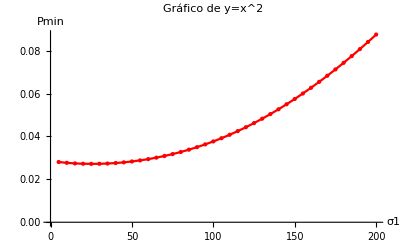

```mathematica
ListPlot[Fig3D1,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```

```mathematica
SubUrbanExpo0={{5,0.10227144954475517},{10,0.10246027831128948},{15,0.10278394640086365},{20,0.1032424526020812},{25,0.10383579517234856},{30,0.1045639727867322},{35,0.10542698434405683},{40,0.10642482887224054},{45,0.10755750549022336},{50,0.10882501339215081},{55,0.11022735183864243},{60,0.11176452015372253},{65,0.11343651771774027},{70,0.11524334396628198},{75,0.11718499839300081},{80,0.11926148052186522},{85,0.12147278994125423},{90,0.12381892627909802},{95,0.12629988920236093},{100,0.1289156784172124},{105,0.13166629366543353},{110,0.13455173472236095},{115,0.13757200139381043},{120,0.14072709351408183},{125,0.14401701082025214},{130,0.1474417534423373},{135,0.1510013211624875},{140,0.15469571391253267},{145,0.15852493162068143},{150,0.16248897425187125},{155,0.16658784177925423},{160,0.17082153418485002},{165,0.17519005148303848},{170,0.17969339364273793},{175,0.18433156068960854},{180,0.18910455266200113},{185,0.1940123695642566},{190,0.19905501144656906},{195,0.20423247833984404},{200,0.2095447702941202}};
SubUrbanExpo50={{5,0.06938503501811352},{10,0.06915816939162844},{15,0.06907261872154877},{20,0.06912721091911556},{25,0.06932119101247805},{30,0.06965420216376751},{35,0.07012625887899392},{40,0.07073771336127004},{45,0.07148921951686757},{50,0.07238170944999645},{55,0.07341633829834464},{60,0.0745944844775313},{65,0.07591765626705452},{70,0.0773874944831319},{75,0.07900569810905164},{80,0.08077398926090994},{85,0.08269404923823881},{90,0.08476743639549682},{95,0.08699556754592146},{100,0.08937957129268274},{105,0.0919202992109047},{110,0.09461816786381322},{115,0.0974731973738806},{120,0.10048469920004564},{125,0.10365176779370582},{130,0.1069727695169111},{135,0.11044564199487326},{140,0.11406790705139432},{145,0.11783676531763852},{150,0.12174919534529624},{155,0.12580206307648303},{160,0.12999225493821737},{165,0.1343167262638121},{170,0.13877263213643862},{175,0.14335735132678976},{180,0.14806855494307966},{185,0.15290421378955024},{190,0.15786261172892174},{195,0.1629423439166619},{200,0.1681422848239238}};
SubUrbanExpo100={{5,0.04511172510556106},{10,0.044919075701072966},{15,0.04482412842504468},{20,0.04482569897128897},{25,0.044922663777551705},{30,0.0451145812230705},{35,0.045401267003074876},{40,0.04578286414669474},{45,0.046259808143081546},{50,0.046832821579523315},{55,0.047502874404237255},{60,0.04827118696823884},{65,0.049139183280773414},{70,0.050108496120821085},{75,0.05118092476709152},{80,0.052358489635021495},{85,0.05364328846264834},{90,0.05503758014077587},{95,0.05654376121125176},{100,0.05816431290733006},{105,0.05990181760981721},{110,0.06175892677736049},{115,0.06373835900134052},{120,0.06584289676291809},{125,0.06807533758393448},{130,0.07043852583800704},{135,0.07293531224804635},{140,0.07556855521064382},{145,0.07834109703428878},{150,0.08125576457245265},{155,0.08431543149910022},{160,0.08752257332440207},{165,0.09088011962773794},{170,0.09439058652281708},{175,0.0980564474144046},{180,0.10188007705959935},{185,0.10586370090261076},{190,0.11000937015833072},{195,0.11431896369582824},{200,0.1187941312067879}};
SubUrbanExpo150={{5,0.03693697664166223},{10,0.03677445232630126},{15,0.03669200822467639},{20,0.036688215697001425},{25,0.03676243195489422},{30,0.03691422539249683},{35,0.037143375908518975},{40,0.037450014374166486},{45,0.03783451054032292},{50,0.038297425865809274},{55,0.0388395700831841},{60,0.039461914138886195},{65,0.04016563514050356},{70,0.04095205854309758},{75,0.04182267348059238},{80,0.042779087432602954},{85,0.043823038078100854},{90,0.04495638863926849},{95,0.04618107629773721},{100,0.0474991311672684},{105,0.04891266936731759},{110,0.05042385936651286},{115,0.0520349247868308},{120,0.05374818023106872},{125,0.05556590624100082},{130,0.05749046016114336},{135,0.059524205075098056},{140,0.061669527336270416},{145,0.06392881026997628},{150,0.06630445072666509},{155,0.06879882859528358},{160,0.07141431866442821},{165,0.07415327674494297},{170,0.07701807521046644},{175,0.08001097934039955},{180,0.08313428684413401},{185,0.08639024226870454},{190,0.08978106197870898},{195,0.09330890738182},{200,0.09697590217863296}};
```

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\SubUrbanExpo0.mat",SubUrbanExpo0];
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\SubUrbanExpo50.mat",SubUrbanExpo50];
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\SubUrbanExpo100.mat",SubUrbanExpo100];
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\SubUrbanExpo150.mat",SubUrbanExpo150];
```